```mathematica
ClearAll["Global`*"];
(* (Wirnik silnika elektrycznego, wykonujący 1000 obr/min, zatrzymuje się po
upływie czasu t od chwili jego wyłączenia. Zakładając, że ruch jest jednostajnie opóźniony,sporządzić wykresy zależności kątowego opóźnienia wirnika i ilości obrotów wykonywanych przez wirnik do chwili zatrzymania się od czasu, dla t=10÷20 s.  *)

n=1000;     (* obr/min *)
```

```mathematica
ωk=0;         (* rad/s *)
```

```mathematica
ωo=(2×π×n)/60;
```

```mathematica
A=Solve[ωk==ϵ×t+ωo,ϵ]
```

{{ϵ→-(100 π)/(3 t)}}

```mathematica
ϕ=ωo×t+(ϵ×t^2)/2/.A

n1=ϕ/(2×π)
```

{(50 π t)/3}

{(25 t)/3}

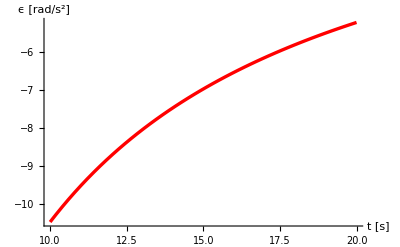

```mathematica
rys1=Plot[ϵ/.A,{t,10,20},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"t [s] ","ϵ [rad/s^2]"}]
```

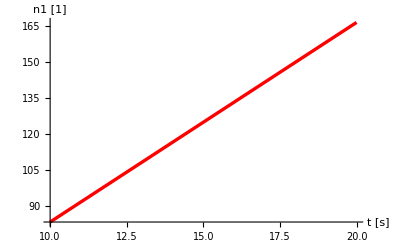

```mathematica
rys1=Plot[n1,{t,10,20},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"t [s] ","n1 [1]"}]
```